King Fahd University of Petroleum and Minerals
Department of Physics
PHYS 210: Methods of Theoretical Physics
Term 212 (Spring 2021-2022)
Instructor: Dr. M. R. Khodja



Term Project

GROUP  #   |  |  | 
  | Student 1  | Student  2 | Student  3
Name |  Mohammed hammadi | Mohammed Alsadah  |  
ID | 201941810  | 201913930  |

# 1. Basics (4)

### Problem 1.1

Calculate the following number

11/3 +217/43+29/551-116/23

#### Solution

```mathematica
11/3+217/43+29/551-116/23
```

209839/56373

### Problem 1.2

Calculate the following number:

11./3 +217/43+29/551-116/23

Note the presence of the decimal point in “11.”.

#### Solution

```mathematica
11./3+217/43+29/551-116/23
```

3.72233

### Problem 1.3

Calculate the exact value of 5^100

#### Solution

```mathematica
5^100
```

7888609052210118054117285652827862296732064351090230047702789306640625

### Problem 1.4

Calculate an approximate value of the number given in Problem 1.3.

#### Solution

```mathematica
5^100//N
```

7.88861×10^69

# 2. Algebra and Trigonometry (9)

### Problem 2.1

Replace x by (2-y) in x^3-x^2+4x

#### Solution

```mathematica
P = x^3-x^2+4x
```

4 x-x^2+x^3

```mathematica
P/.x->(2-y)
```

4 (2-y)-(2-y)^2+(2-y)^3

### Problem 2.2

Expand out products and powers in the above result.

#### Solution

```mathematica
Expand[%]
```

12-12 y+5 y^2-y^3

### Problem 2.3

Define function f such that f(x)=a x^3 sin(a x).

#### Solution

```mathematica
f[x_]:= a x^3 Sin[a x]
```

### Problem 2.4

Use the above-defined function f to evaluate f(√2).

#### Solution

```mathematica
f[Sqrt[2]]
```

2 √2 a Sin[√2 a]

### Problem 2.5

(1) Clear the definition assigned to symbol f in Problem 2.3. (2) Confirm that the definition of f has been cleared by caculating f(√2) again and comparing the result with the answer of Problem 2.4.

#### Solution

```mathematica
Clear[f]
```

```mathematica
f[Sqrt[2]]
```

f[√2]

different from 2.4

### Problem 2.6

Solve the algebraic equation of second order a x^2+b x+c=0.

#### Solution

```mathematica
Solve[a x^2+b x +c==0,x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

### Problem 2.7

Find the exact solution(s) to the following algebraic equation:

√(x-1)+√x+√(x+1)=3

#### Solution

```mathematica
Solve[Sqrt[x-1]+Sqrt[x]+Sqrt[x+1]==3,x]
```

{{x→7-2/3 √(10+(14 2^(2/3))/(41+9 ⅈ √47)^(1/3)+(2 (41+9 ⅈ √47))^(1/3))-1/2 √(320/9-(224 2^(2/3))/(9 (41+9 ⅈ √47)^(1/3))-16/9 (2 (41+9 ⅈ √47))^(1/3)+64/(√(10+(14 2^(2/3))/(41+9 ⅈ √47)^(1/3)+(2 (41+9 ⅈ √47))^(1/3))))}}

### Problem 2.8

The solution to the algebraic equation in Problem 2.7 is real. However, Mathematica cannot simplify the result. Show this by solving the equation numerically.

#### Solution

```mathematica
NSolve[Sqrt[x-1]+Sqrt[x]+Sqrt[x+1]==3,x]
```

{{x→1.1866}}

### Problem 2.9

Transcendental (i.e., non-algebraic) equations cannot be solved with Mathematica commands Solve, NSolve, and Reduce. (1) Confirm this by trying to solve the following transcendental equation: cos(x)=x using these commands. (2) Find the appropriate Mathematica command for solving the equation.

#### Solution

```mathematica
Solve[Cos[x]==x,x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[Cos[x]==x,x]

```mathematica
NSolve[Cos[x]==x,x]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[Cos[x]==x,x]

```mathematica
Reduce[Cos[x]==x,x]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[Cos[x]==x,x]

```mathematica
FindRoot[Cos[x]==x,{x,100}]
```

{x→0.739085}

# 3. Plots and Animations (15)

## Simple 2D Plots

### Problem 3.1

Define a function f such that f(x)=e^-x then plot f(x) for x ∈ [0,3].

#### Solution

```mathematica
f[x_]:= E^(-x)
```

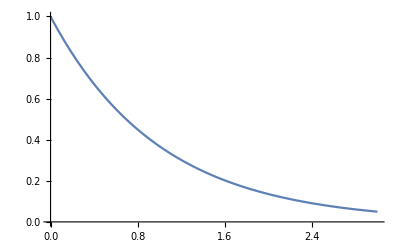

```mathematica
Plot[f[x],{x,0,3}]
```

## List Plots

### Problem 3.2

Define a function f such that f(x)=e^-x then plot f(x) for x ∈ [0,3].

#### Solution

```mathematica
f[x_]:= E^(-x)
```

```mathematica
Plot[f[x],{x,0,3}]
```

-Graphics-

### Problem 3.3

Define a list that contains the following set of data points

{{1,2},{2,4},{3,5},{4,5},{5,4},{6,3},{7,2.5}}

then plot the data points

#### Solution

```mathematica
S={{1,2},{2,4},{3,5},{4,5},{5,4},{6,3},{7,2.5}}
```

{{1,2},{2,4},{3,5},{4,5},{5,4},{6,3},{7,2.5}}

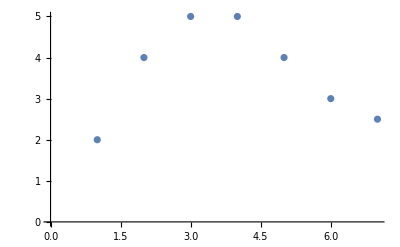

```mathematica
ListPlot[S]
```

### Problem 3.4

Plot the list of data points defined in Problem 3.2 as joined points.

#### Solution

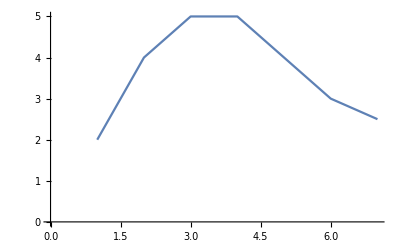

```mathematica
ListPlot[S,Joined->True]
```

## Parametric Plots

### Problem 3.5

A circle can be represented parametrically by

x(ϕ) = sin(ϕ),
y(ϕ) = cos(ϕ)

Use the Mathematica ParametricPlot command to plot this circle for ϕ  ∈ [0, 2π].

#### Solution

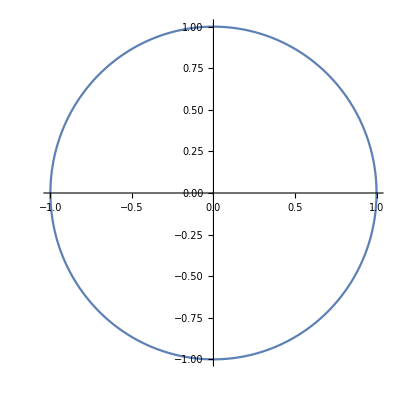

```mathematica
ParametricPlot[{Sin[ϕ],Cos[ϕ]},{ϕ,0,2Pi}]
```

### Problem 3.6

Plot parametrically the cycloid defined by

x(ϕ)=sin(ϕ)+1/2 ϕ,
y(ϕ)=cos(ϕ);

for ϕ  ∈ [0, 4π].

#### Solution

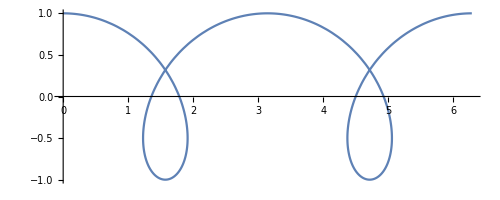

```mathematica
ParametricPlot[{Sin[ϕ]+0.5ϕ,Cos[ϕ]},{ϕ,0,4Pi}]
```

## 3D Plots

### Problem 3.7

Plot the following plane wave

A cos((2π)/T t-(2π)/λ x)

for x ∈ [0, 2λ] and t x ∈ [0, 2T]. Hint: Give parameters A, T, and λ numerical values. For instance, let A=T=λ=1.

#### Solution

```mathematica
λ = A = T = 1
```

1

```mathematica
F[t_,x_] = A Cos[(2π)/T t-(2π)/λ x]
```

Cos[2 π t-2 π x]

```mathematica
Plot3D[F[t,x], {t, 0,2T } , {x , 0 , 2λ}]
```

-Graphics3D-

## Contour Plots

### Problem 3.8

Plot a contour plot of the plane wave of Problem 3.6.

#### Solution

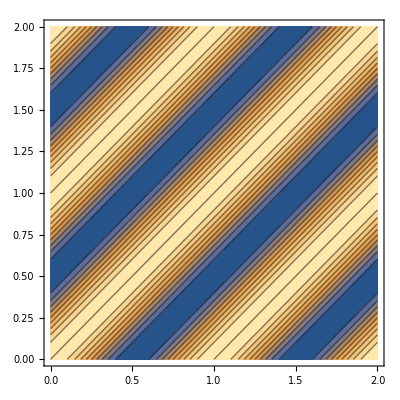

```mathematica
ContourPlot[F[t,x], {t, 0,2T } , {x , 0 , 2λ}]
```

### Problem 3.9

The electric potential at point (x,y) due to a positive, unit charge located at point (x_i,y_i) is given by the following function:

V(x,y)=(8.988×10^9)/(√((x-x)^2+(y-y)^2))

Consider a system of three positive, unit charges forming an equilateral triangle and located at

x_1=0,   y_1=1/(√3),
x_2=-1/2,   y_2=-1/(2 √3),
x_3=1/2,   y_3=-1/(2 √3).

Then, the electric potential due to the system at point (x,y) will be given by

V(x-x_1,y-y_1)+V(x-x_2,y-y_2)+V(x-x_3,y-y_3).

Plot the equipotential lines corresponding to this system of charges for x ∈ [-1, +1] and y ∈ [-1, +1]. 
Hint: Set the number of contour lines to 15.

#### Solution

```mathematica
Subscript[x, 1]=0
```

0

```mathematica
Subscript[y, 1]=1/(√3)
```

1/(√3)

```mathematica
Subscript[x, 2]=-1/2
```

-1/2

```mathematica
Subscript[y, 2]=-1/(2 √3)
```

-1/(2 √3)

```mathematica
Subscript[x, 3]=1/2
```

1/2

```mathematica
Subscript[y, 3]=-1/(2 √3)
```

-1/(2 √3)

```mathematica
V[x_,y_]=(8.988×10^9)/(√((x- Subscript[x, i])^2+(y- Subscript[y, i])^2))
```

(8.988×10^9)/(√((x-x_i)^2+(y-y_i)^2))

```mathematica
V[x,y]/.{x->x-Subscript[x, 1],y->y-Subscript[y, 1], Subscript[x, i]-> Subscript[x, 1],Subscript[y, i]-> Subscript[y, 1]}
```

(8.988×10^9)/(√(x^2+(-2/(√3)+y)^2))

```mathematica
Subscript[V, 1]=%
```

(8.988×10^9)/(√(x^2+(-2/(√3)+y)^2))

```mathematica
V[x,y]/.{x->x-Subscript[x, 2],y->y-Subscript[y, 2], Subscript[x, i]-> Subscript[x, 2],Subscript[y, i]-> Subscript[y, 2]}
```

(8.988×10^9)/(√((1+x)^2+(1/(√3)+y)^2))

```mathematica
Subscript[V, 2]=%
```

(8.988×10^9)/(√((1+x)^2+(1/(√3)+y)^2))

```mathematica
V[x,y]/.{x->x-Subscript[x, 3],y->y-Subscript[y, 3], Subscript[x, i]-> Subscript[x, 3],Subscript[y, i]-> Subscript[y, 3]}
```

(8.988×10^9)/(√((-1+x)^2+(1/(√3)+y)^2))

```mathematica
Subscript[V, 3]=%
```

(8.988×10^9)/(√((-1+x)^2+(1/(√3)+y)^2))

```mathematica
S = Subscript[V, 1]+Subscript[V, 2]+Subscript[V, 3]
```

(8.988×10^9)/(√(x^2+(-2/(√3)+y)^2))+(8.988×10^9)/(√((-1+x)^2+(1/(√3)+y)^2))+(8.988×10^9)/(√((1+x)^2+(1/(√3)+y)^2))

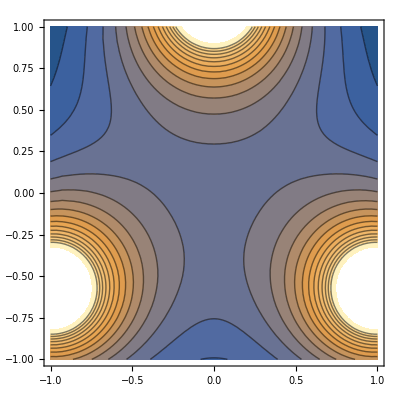

```mathematica
ContourPlot[S,{x,-1,1},{y,-1,1},Contours->15]
```

## 3D Parametric Plots

### Problem 3.10

Curves in 3D space can be represented with the help of one parameter. Plot a 3D parametric plot of the following helix parameterized by u. Let u ∈ [0,20].

x(u) = sin(u);
y(u) = cos(u);
z(u) = u/10;

#### Solution

```mathematica
ParametricPlot3D[{Sin[u],Cos[u],u/10},{u,0,20}]
```

-Graphics3D-

### Problem 3.11

Surfaces in 3D space can be represented with the help of two parameters. Plot a 3D parametric plot of the following torus parameterized by u and v. Let u ∈ [0,2π] and v ∈ [0,2π].

R = 3;   r = 1.5;
x(u,v) = (R + r cos(v)) sin(u);
y(u,v) = (R + r cos(v)) cos(u);
z(u,v) = r sin(v);

R is the distance from the origin of coordinates to the center of the torus. r is the distance from the center of the torus to its surface. You can use the following values R = 3,   r = 1.

#### Solution

```mathematica
R=3
```

3

```mathematica
r=1.5
```

1.5

```mathematica
x[u_,v_]= (R + r Cos[v]) Sin[u]
```

(3+1.5 Cos[v]) Sin[u]

```mathematica
y[u_,v_]= (R + r Cos[v]) Cos[u]
```

Cos[u] (3+1.5 Cos[v])

```mathematica
z[u_,v_]= r Sin[v]
```

1.5 Sin[v]

```mathematica
ParametricPlot3D[{x[u,v],y[u,v],z[u,v]},{u,0,2Pi},{v,0,2Pi}]
```

-Graphics3D-

## Animations

### Problem 3.12

Use the Manipulate command to generate a plot of the following harmonic functions and their sum that can be controlled through the value of the phase ϕ_0

Q_1(t)=sin(2π  t)
Q_2(t,ϕ_0)=sin(2π  t+ϕ_0)

Hint: Let ϕ_0 ∈ [-π, π] and t ∈ [0, 3].

#### Solution

```mathematica
Subscript[Q, 1][t_]=Sin[2Pi  t]
```

Sin[2 π t]

```mathematica
Subscript[Q, 2][t_,Subscript[ϕ, 0]_]=Sin[2Pi  t+Subscript[ϕ, 0]]
```

Sin[2 π t+ϕ_0]

```mathematica
Manipulate[Plot[{Subscript[Q, 1][t],Subscript[Q, 2][t,Subscript[ϕ, 0]],Subscript[Q, 1][t]+Subscript[Q, 2][t,Subscript[ϕ, 0]]},{t,0,3},PlotRange->{{0,Pi},{-2,2}}],{Subscript[ϕ, 0],-Pi,Pi}]
```

### Problem 3.13

Use the Manipulate command to generate a plot of the torus given in Problem 3.11 that can be controlled through the values of R and r.

#### Solution

```mathematica
Clear[R,r]
```

```mathematica
x[u_,v_,R_,r_]= (R + r Cos[v]) Sin[u]
```

(R+r Cos[v]) Sin[u]

```mathematica
y[u_,v_,R_,r_]= (R + r Cos[v]) Cos[u]
```

Cos[u] (R+r Cos[v])

```mathematica
z[u_,v_,R_,r_]= r Sin[v]
```

r Sin[v]

```mathematica
Manipulate[ParametricPlot3D[{x[u,v,R,r],y[u,v,R,r],z[u,v,R,r]},{u,0,2Pi},{v,0,2Pi}],{R,0,5},{r,0,5}]
```

### Problem 3.14

Use the Animate command to generate an animation of the plot of the following two Gaussian pulses and their sum

G_1(x,t)=ⅇ^(-(x+6-t)^2),
G_2(x,t)=1/2 ⅇ^(-(x+6-t)^2).

Hint: Let the control parameter be t ∈ [0,10] and let x ∈ [-4,4].

#### Solution

```mathematica
Subscript[G, 1][x_,t_]= E^(-(x+6-t)^2)
```

ⅇ^(-(6-t+x)^2)

```mathematica
Subscript[G, 2][x_,t_]= 0.5E^(-(x+6-t)^2)
```

0.5 ⅇ^(-(6-t+x)^2)

```mathematica
Animate[Plot[{Subscript[G, 1][x,t],Subscript[G, 2][x,t],Subscript[G, 1][x,t]+Subscript[G, 2][x,t]},{x,-4,4},PlotRange->{0,1.5}],{t,0,10}]
```

### Problem 3.15

Use the Animate command to generate an animation of the plot of the following surface

S(x,y,t) = Cos(x + y - t).

Let the control parameter be t.

#### Solution

```mathematica
S[x,y,t]=Cos[x+y-t]
```

Cos[t-x-y]

```mathematica
Animate[Plot3D[S[x,y,t],{x,-2Pi,2Pi},{y,-2Pi,Pi}],{t,-2Pi,2Pi}]
```

# 4. Series (4)

### Problem 4.1

Use Mathematica to test the convergence of the following series.

∑_(n=0)^∞ 1/2^n,
∑_(n=0)^∞ (1+n)/2^(a n),
∑_(n=0)^∞ (sin(n))/2^n,
∑_(n=1)^∞ (-1)^n/n,
∑_(n=1)^∞ ((1+i)/(2-i))^n,
∑_(n=1)^∞ (1+ⅈ)^n,
∑_(n=1)^∞ (Log[n]Sin[n])/2^n

Hint: Try to perform a direct compuation of the sum.

#### Solution

```mathematica
Sum[1/2^n,{n,0,Infinity}]
```

2

```mathematica
Sum[(1+n)/2^(a n),{n,0,Infinity}]
```

2^(2 a)/((-1+2^a)^2)

```mathematica
Sum[Sin[n]/2^n,{n,0,Infinity}]
```

(2 Sin[1])/(5-4 Cos[1])

```mathematica
Sum[(-1)^n/n,{n,1,Infinity}]
```

-Log[2]

```mathematica
Sum[((1+I)/(2-I))^n,{n,1,Infinity}]
```

-1/5+(3 ⅈ)/5

```mathematica
Sum[(1+I)^n,{n,1,Infinity}]
```

Sum::div: Sum does not converge.

∑_(n=1)^∞ (1+ⅈ)^n

```mathematica
Sum[Log[n]Sin[n]/(2)^n,{n,1,Infinity}]
```

∑_(n=1)^∞ 2^-n Log[n] Sin[n]

### Problem 4.2

In Problem 4.1, Mathematica was unable to calculate the exact sum of the last series, i.e., ∑_(n=1)^∞ (Log[n]Sin[n])/2^n. Mathematica can do it numerically, though. Calculate this sum numerically.

#### Solution

```mathematica
NSum[Log[n]Sin[n]/(2)^n,{n,1,Infinity}]
```

0.0727061

### Problem 4.3

Expand the following funtions as Mclaurin power series (i.e., Taylor series about the origin) to order 10. Compare your results for the first 5 funtions with eqs. 13.1, 13.2, 13.3, 13.4, 13.5 in the textbook.

sin(x),
cos(x),
e^x,
ln(1+x),
(1+x)^p, 
(e^(-x^2))/(√(1+x^2))sin(5x)

#### Solution

```mathematica
Series[Sin[x],{x,0,10}]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880+O[x]^11

```mathematica
Series[Cos[x],{x,0,10}]
```

1-x^2/2+x^4/24-x^6/720+x^8/40320-x^10/3628800+O[x]^11

```mathematica
Series[E^x,{x,0,10}]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800+O[x]^11

```mathematica
Series[Log[1+x],{x,0,10}]
```

x-x^2/2+x^3/3-x^4/4+x^5/5-x^6/6+x^7/7-x^8/8+x^9/9-x^10/10+O[x]^11

```mathematica
Series[(1+x)^p,{x,0,10}]
```

1+p x+1/2 (-1+p) p x^2+1/6 (-2+p) (-1+p) p x^3+1/24 (-3+p) (-2+p) (-1+p) p x^4+1/120 (-4+p) (-3+p) (-2+p) (-1+p) p x^5+1/720 (-5+p) (-4+p) (-3+p) (-2+p) (-1+p) p x^6+((-6+p) (-5+p) (-4+p) (-3+p) (-2+p) (-1+p) p x^7)/5040+((-7+p) (-6+p) (-5+p) (-4+p) (-3+p) (-2+p) (-1+p) p x^8)/40320+((-8+p) (-7+p) (-6+p) (-5+p) (-4+p) (-3+p) (-2+p) (-1+p) p x^9)/362880+((-9+p) (-8+p) (-7+p) (-6+p) (-5+p) (-4+p) (-3+p) (-2+p) (-1+p) p x^10)/3628800+O[x]^11

```mathematica
Series[E^(-x^2)Sin[5x]/(Sqrt[1+x^2]),{x,0,10}]
```

5 x-(85 x^3)/3+(385 x^5)/6-(5590 x^7)/63+(59575 x^9)/648+O[x]^11

### Problem 4.4

Consider the following function

f(x) = ArcTan(x).

(1) Define the following Taylor series expansions of f(x)

T1(x) = Taylor series expansion at x=0 to 1st order
T3(x) = Taylor series expansion at x=0 to 3rd order
T5(x) = Taylor series expansion at x=0 to 5th order
T7(x) = Taylor series expansion at x=0 to 7th order

Show in a single plot the graphs of f(x), T1(x), T3(x), T5(x), T7(x). Let x ∈ [0,5] and the plot range [0,2]. Observe how the Taylor expansions T1(x), T3(x), T5(x), T7(x) have a range of convergence |x|<1. Outside this range, the expansions do not provide an approximation to f(x), whatever the order

(2) Define the following large-x Taylor series expansions of f(x)

A1(x) = large-x Taylor series expansion to 1st order
A3(x) = large-x Taylor series expansion to 3rd order
A5(x) = large-x Taylor series expansion to 5th order
A7(x) = large-x Taylor series expansion to 7th order

Show in a single plot the graphs of f(x), A1(x), A3(x), A5(x), A7(x). Let x ∈ [0,5] and the plot range [0,2]. Observe how the large-x Taylor expansions A1(x), A3(x), A5(x), A7(x) have a range of convergence |x|>1. Outside this range, the expansions do not provide an approximation to f(x), whatever the order.
Hint: (1) Use the Mathematica command Normal to convert the outputs of the Series command into expressions that Mathematica can plot. (2) Choose a plot style that distinguished between the curves. Eg., you can use PlotStyle→{Thick,Dashed,Dashed,Dashed,Dashed}. (3) Large-x Taylor series expansions are sometimes called expansions at infinity.

#### Solution

```mathematica
f[x_]= ArcTan[x]
```

ArcTan[x]

```mathematica
T1[x_]=  Series[f[x],{x,0,1}]
```

x+O[x]^2

```mathematica
T3[x_]=  Series[f[x],{x,0,3}]
```

x-x^3/3+O[x]^4

```mathematica
T5[x_]=  Series[f[x],{x,0,5}]
```

x-x^3/3+x^5/5+O[x]^6

```mathematica
T7[x_]=  Series[f[x],{x,0,7}]
```

x-x^3/3+x^5/5-x^7/7+O[x]^8

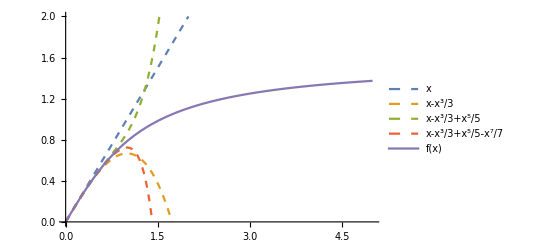

```mathematica
Plot[{Evaluate[Normal[T1[x]]],Evaluate[Normal[T3[x]]],Evaluate[Normal[T5[x]]],Evaluate[Normal[T7[x]]],f[x]},{x,0,5},PlotRange->{0,2},PlotLegends->"Expressions",PlotStyle->{Dashed,Dashed,Dashed,Dashed,Thick}]
```

```mathematica
A1[x_]= Series[f[x],{x,Infinity,1}]
```

π/2-1/x+O[1/x]^2

```mathematica
A3[x_]= Series[f[x],{x,Infinity,3}]
```

π/2-1/x+1/(3 x^3)+O[1/x]^4

```mathematica
A5[x_]= Series[f[x],{x,Infinity,5}]
```

π/2-1/x+1/(3 x^3)-1/(5 x^5)+O[1/x]^6

```mathematica
A7[x_]= Series[f[x],{x,Infinity,7}]
```

π/2-1/x+1/(3 x^3)-1/(5 x^5)+1/(7 x^7)+O[1/x]^8

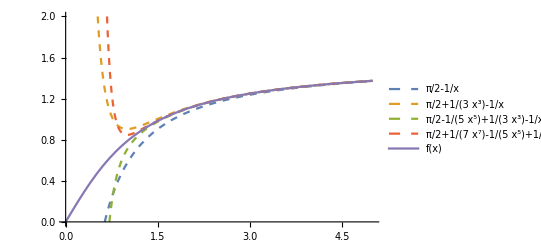

```mathematica
Plot[{Evaluate[Normal[A1[x]]],Evaluate[Normal[A3[x]]],Evaluate[Normal[A5[x]]],Evaluate[Normal[A7[x]]],f[x]},{x,0,5},PlotRange->{0,2},PlotLegends->"Expressions",PlotStyle->{Dashed,Dashed,Dashed,Dashed,Thick}]
```

### Problem 4.4

Taylor series expansions can be generalized for functions of many variables. Consider the following function:

f(x,y) = sin(x+y)

(1) Find the Taylor series expansion of f at x=0 to 3rd order. 
(2) Find the Taylor series expansion of f at x=0=y to 3rd order.

#### Solution

```mathematica
f[x_,y_]= Sin[x+y]
```

Sin[x+y]

```mathematica
Series[f[x,y],{x,0,3}]
```

Sin[y]+Cos[y] x-1/2 Sin[y] x^2-1/6 Cos[y] x^3+O[x]^4

```mathematica
Series[f[x,y],{x,0,3},{y,0,3}]
```

(y-y^3/6+O[y]^4)+(1-y^2/2+O[y]^4) x+(-y/2+y^3/12+O[y]^4) x^2+(-1/6+y^2/12+O[y]^4) x^3+O[x]^4

# 5. Complex Numbers (4)

### Problem 5.1

Using Mathematica, find the real and imaginary parts of the following complex numbers:

(2-i)(3+2i),
(1+2 i)/(3-4i)+(2-i)/(5i),
(1/((1-i)(2-i)(3-i)))^(1/3),
((1+i √3)/(√3+ i))^217.c

#### Solution

(2-i)(3+2i)

The real part of (2-i)(3+2i) is

```mathematica
Re[(2-I)(3+2I)]
```

8

The imaginary part of (2-i)(3+2i) is

```mathematica
Im[(2-I)(3+2I)]
```

1

(1+2 i)/(3-4i)+(2-i)/(5i)

The real part of (1+2 i)/(3-4i)+(2-i)/(5i) is

```mathematica
Re[ (1+2 I)/(3-4 I)+(2-I)/(5I)]
```

-2/5

The imaginary part of (1+2 i)/(3-4i)+(2-i)/(5i)is

```mathematica
Im[ (1+2 I)/(3-4 I)+(2-I)/(5I)]
```

0

(1/((1-i)(2-i)(3-i)))^(1/3)

The real part of (1/((1-i)(2-i)(3-i)))^(1/3) is

```mathematica
Re[(1/((1-I)(2-I)(3-I)))^(1/3)]
```

(√3)/(2 10^(1/3))

The imaginary part of (1/((1-i)(2-i)(3-i)))^(1/3) is

```mathematica
Im[(1/((1-I)(2-I)(3-I)))^(1/3)]
```

1/(2 10^(1/3))

((1+i √3)/(√3+ i))^217

The real part of ((1+i √3)/(√3+ i))^217 is

```mathematica
Re[((1+I √3)/(√3+ I))^217]
```

(√3)/2

The imaginary part of ((1+i √3)/(√3+ i))^217 is

```mathematica
Im[((1+I √3)/(√3+ I))^217]
```

1/2

### Problem 5.2

Using Mathematica, convert the complex numbers given in Problem 5.1 to polar form (i.e., find the absolute values and the arguments of the numbers).

#### Solution

|(2-i)(3+2i)| =

```mathematica
Abs[(2-I)(3+2I)]
```

√65

argument of (2-i)(3+2i)

```mathematica
Arg[(2-I)(3+2I)]
```

```mathematica
ArcTan[1./8]
```

0.124355

ArcTan[1/8]

|(1+2 i)/(3-4i)+(2-i)/(5i)| =

```mathematica
Abs[(1+2 I)/(3-4I)+(2-I)/(5I)]
```

2/5

argument of (1+2 i)/(3-4i)+(2-i)/(5i)

```mathematica
Arg[(1+2 I)/(3-4 I)+(2-I)/(5I)]
```

π

|(1/((1-i)(2-i)(3-i)))^(1/3)| =

```mathematica
Abs[(1/((1-I)(2-I)(3-I)))^(1/3)]
```

1/10^(1/3)

argument of (1/((1-i)(2-i)(3-i)))^(1/3)

```mathematica
Arg[(1/((1-I)(2-I)(3-I)))^(1/3)]
```

π/6

|((1+i √3)/(√3+ i))^217|=

```mathematica
Abs[((1+I √3)/(√3+ I))^217]
```

1

argument of ((1+i √3)/(√3+ i))^217

```mathematica
Arg[((1+I √3)/(√3+ I))^217]
```

π/6

### Problem 5.3

By default, all symbols in Mathematica are complex. Show this by using the Re and Im commands to calculate the real and imaginary parts of z = u + i  v  .

#### Solution

```mathematica
u = 10 
v = 20
```

10

20

```mathematica
Re[u + v I]
```

10

```mathematica
Im[u + I v]
```

20

### Problem 5.4

Take the complex number z = u + i  v defined in Problem 5.3. Show that by using the Mathematica Simplify command and declaring u and v as real quantities with the Assumptions option, Re and Im  give the expected results.

#### Solution

# 6. Systems of Linear Equations (2)

### Problem 6.1

Use the Mathematica command Solve to solve the following system of linear equations:

a-3b+c==0
a+b+2c==-1
2a+b-c==2

#### Solution

```mathematica
Solve[a-3b+c == 0  && a+b+2c == -1 && 2a+b-c == 2 , {a, b , c}]
```

{{a→12/19,b→-1/19,c→-15/19}}

### Problem 6.2

Use the Mathematica command LinearSolve to solve the same system of linear equations given in Problem 6.1 in matrix form. Compare the result with the solution of Problem 6.1.

#### Solution

```mathematica
m = ({{1, -3, 1}, {1, 1, 2}, {2, 1, -1}})
b = ({{0}, {-1}, {2}})
```

{{1,-3,1},{1,1,2},{2,1,-1}}

{{0},{-1},{2}}

```mathematica
LinearSolve[m,b]
```

{{12/19},{-1/19},{-15/19}}

# 7. Vectors and Matrices (19)

## Vector Calculations

### Problem 7.1

Calculate the scalar product of the following two vectors

aVec = {a1, a2, a3};
bVec = {b1, b2, b3};

#### Solution

```mathematica
aVec = {a1, a2, a3} 
bVec = {b1, b2, b3}
```

{a1,a2,a3}

{b1,b2,b3}

```mathematica
aVec . bVec
```

a1 b1+a2 b2+a3 b3

### Problem 7.2

Using the appropriate Mathematica command, calculate (1) the exact value and (2) the numerical value of the angle between the following pairs of vectors:

{1, 0} and {1, 1};
{1/2, (-5 √2)/3,6} and {-1, +1,10}

#### Solution

```mathematica
VectorAngle[{1,0} , {1,1}]
```

π/4

```mathematica
VectorAngle[N[{1,0}] , N[{1,1}]]
```

0.785398

```mathematica
VectorAngle[{1/2,(-5 √2)/3,6} , {-1,+1,10}]
```

ArcCos[√(6/25585) (119/2-(5 √2)/3)]

```mathematica
VectorAngle[N[{1/2,(-5 √2)/3,6} ], N[{-1,+1,10}]]
```

0.505203

### Problem 7.3

Calculate the vector cross product of the vectors given in Problem 7.1.

#### Solution

```mathematica
Cross[aVec, bVec]
```

{-a3 b2+a2 b3,a3 b1-a1 b3,-a2 b1+a1 b2}

### Problem 7.4

Using the vectors defined in Problem 7.1, check that the scalar product is symmetric and the vector cross product is antisymmetric. Hint: The product * of A and B is symmetric when A*B=B*A; It is antisymmetric when A*B=-B*A.

#### Solution

```mathematica
aVec . bVec == bVec . aVec
```

True

```mathematica
result1 = Cross[aVec , bVec]
result2 = Cross[bVec , aVec]
```

{-a3 b2+a2 b3,a3 b1-a1 b3,-a2 b1+a1 b2}

{a3 b2-a2 b3,-a3 b1+a1 b3,a2 b1-a1 b2}

### Problem 7.5

Show that when A is a vector, Mathematica distinguishes between √(A·A) and √(A^2).

#### Solution

```mathematica
A = {a1, a2}
Sqrt[A . A]
```

{a1,a2}

√(a1^2+a2^2)

```mathematica
Sqrt[A^2]
```

{√(a1^2),√(a2^2)}

### Problem 7.6

The mixed vector product is a dot product of a vector and a cross product of two other vectors such as A·(B×C). Check that the mixed vector product is invariant with respect to the cyclic permutations of the three vectors, that is, A·(B×C)=C·(A×B)=B·(C×A). Hint: Define 3 vectors (see Problem 7.1) and use the Simplify command to ensure that the answer is in its simplest form.

#### Solution

```mathematica
A=  {a1 , a2 , a3}
B = {b1 , b2 , b3}
c = {c1 , c2 , c3}
```

{a1,a2,a3}

{b1,b2,b3}

{c1,c2,c3}

```mathematica
Simplify[A . Cross[B , c]] == Simplify[c . Cross[A, B]]  == Simplify[B . Cross[c , A]]
```

True

### Problem 7.7

Check the double cross product identity, that is

A×(B×C)≡B(A·C)-C(A·B)

#### Solution

```mathematica
Cross[A , Cross[B, c]]
```

{-a2 b2 c1-a3 b3 c1+a2 b1 c2+a3 b1 c3,a1 b2 c1-a1 b1 c2-a3 b3 c2+a3 b2 c3,a1 b3 c1+a2 b3 c2-a1 b1 c3-a2 b2 c3}

```mathematica
Cross[B , (A . c)] - Cross[c, (A . B)]
```

{b1,b2,b3}×(a1 c1+a2 c2+a3 c3)-{c1,c2,c3}×(a1 b1+a2 b2+a3 b3)

### Problem 7.8

The Table command can be used to authomatically generate the components of a vector. Use Mathematica to find the 7th component of the following vector

tab=Table[i^2,{i,5,15}].

#### Solution

```mathematica
tab=Table[i^2,{i,5,15}]
```

{25,36,49,64,81,100,121,144,169,196,225}

## Vector Plots

### Problem 7.9

Vector functions of scalar arguments can be plotted with the Mathematica commands VectorPlot, StreamPlot (in 2D) VectorPlot3D (in 3D), as well as with other commands. Using VectorPlot and StreamPlot plot the normalized electric field of a unit, positive charge given by

4π ϵ_0 E(r)=r/r^3

in the x-y plane (z = 0) where x ∈ [-1,+1] and y ∈ [-1,+1]. Hint: (1) since we are interesting only in the field in the x-y plane, we can ignore its z-component and plot only its x- and y-components which leaves us with a 2D function. (2) With VectorPlot you can use 9 for the VectorPoints option; with StreamPlot you can use 100 for the StreamPoints option.

#### Solution

#### Solution

```mathematica
ϵ = 8.854187817×10^(-12)
```

8.85419×10^-12

```mathematica
8.854187816999999*^-12
```

8.85419×10^-12

```mathematica
ElectricFeild  = {x , y}/(4 * Sqrt[x^2 + y ^2] ^ 3 * Pi * ϵ)
```

{(8.98755×10^9 x)/((x^2+y^2)^(3/2)),(8.98755×10^9 y)/((x^2+y^2)^(3/2))}

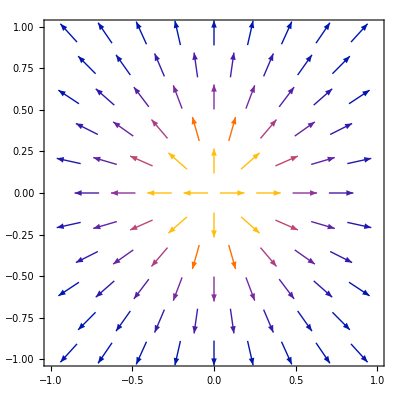

```mathematica
VectorPlot[ElectricFeild   , {x , -1 , 1} , {y , -1 , 1} , VectorPoints->9]
```

### Problem 7.10

Repeat Problem 7.9 for the following field:

vecField={-x^2+y-1,x-y^2+1}

where x ∈ [-3,+3] and y ∈ [-3,+3]

Hint: You can use 10 for the VectorPoints option and 100 for the StreamPoints option.

#### Solution

{-1-x^2+y,1+x-y^2}

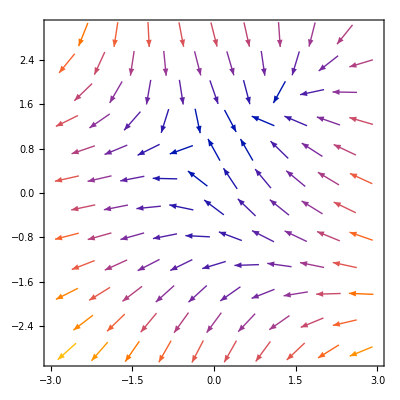

```mathematica
vecField={-x^2+y-1,x-y^2+1} 
VectorPlot[vecField , {x , -3 , 3} , {y , -3 ,3 } , VectorPoints-> 10]
```

### Problem 7.11

Plot the 3D vector plot of the normalized electric field created by two charges with unit magnitude and opposite signs. Let the positive charge be at point (1,1,1) and the negative charge be at point (-1,-1,-1). Hint: You can use 9 for the VectorPoints option and 0.3 for the VectorScale option.

#### Solution

```mathematica
q1 = 1
q2 = -1
```

1

-1

```mathematica
ElectricField ={ q1/(4 * Pi * ϵ * (x - 1)^ 2) + q2/(4 *Pi * ϵ *(x + 1)^ 2) , q1/(4 *Pi * ϵ *(y - 1)^ 2) + q2/(4 *Pi * ϵ *(y + 1)^ 2), q1/(4 *Pi * ϵ *(z - 1)^ 2) + q2/(4 *Pi * ϵ *(z +1)^ 2)}
```

{(8.98755×10^9)/(-1+x)^2-(8.98755×10^9)/(1+x)^2,(8.98755×10^9)/(-1+y)^2-(8.98755×10^9)/(1+y)^2,(8.98755×10^9)/(-1+z)^2-(8.98755×10^9)/(1+z)^2}

```mathematica
VectorPlot3D[ElectricField , {x , -3 , 3} , {y , -3 , 3} , {z , -3, 3} , VectorPoints->9 , VectorScaling->0.3]
```

```mathematica
ElectricField2 ={q1/(4 * Pi * ϵ * (x - 1)^ 2) + q2/(4 *Pi * ϵ *(x + 1)^ 2)  , q1/(4 *Pi * ϵ *(y - 1)^ 2) + q2/(4 *Pi * ϵ *(y + 1)^ 2)}
```

{(8.98755×10^9)/(-1+x)^2-(8.98755×10^9)/(1+x)^2,(8.98755×10^9)/(-1+y)^2-(8.98755×10^9)/(1+y)^2}

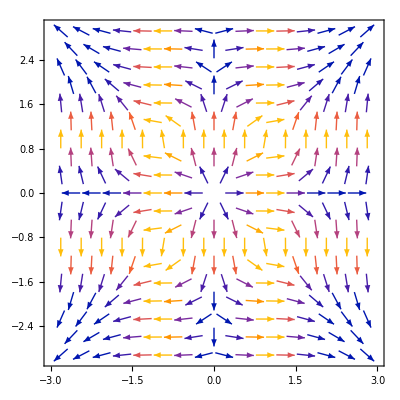

```mathematica
VectorPlot[ElectricField2, {x , -3 , 3} , {y , -3 , 3}  ]
```

## Matrix Calculations

### Problem 7.12

Use Mathematica to extract (1) the first row (2) the 2nd column, and (3) entry m1_34 of the following matrix:

m1=(1 | 1 | 0 | -1
-2 | 0 | 3 | 0
1 | 2 | -3 | 2
2 | 1 | 0 | -2);

#### Solution

```mathematica
m1=({{1, 1, 0, -1}, {-2, 0, 3, 0}, {1, 2, -3, 2}, {2, 1, 0, -2}})

m1[[1]]
Indexed[m1, {3,4}]
```

{{1,1,0,-1},{-2,0,3,0},{1,2,-3,2},{2,1,0,-2}}

{1,1,0,-1}

2

### Problem 7.13

(1) Multiply the following two matrices:

m1=(1 | 1 | 0 | -1
-2 | 0 | 3 | 0
1 | 2 | -3 | 2
2 | 1 | 0 | -2);
m2=(2 | -5 | -1 | 2
0 | 3 | -2 | 3
3 | -2 | 1 | 0
1 | 1 | 1 | 1);

(2) Output the result in matrix form.

#### Solution

```mathematica
m1=({{1, 1, 0, -1}, {-2, 0, 3, 0}, {1, 2, -3, 2}, {2, 1, 0, -2}})
m2=({{2, -5, -1, 2}, {0, 3, -2, 3}, {3, -2, 1, 0}, {1, 1, 1, 1}})
m3 = m1 . m2
```

{{1,1,0,-1},{-2,0,3,0},{1,2,-3,2},{2,1,0,-2}}

{{2,-5,-1,2},{0,3,-2,3},{3,-2,1,0},{1,1,1,1}}

{{1,-3,-4,4},{5,4,5,-4},{-5,9,-6,10},{2,-9,-6,5}}

### Problem 7.14

Using the two matrices in Problem 7.13, confirm that

detAB = detBA = detA detB

#### Solution

```mathematica
m4 = m2 . m1
```

{{15,2,-12,-8},{-2,-1,15,-10},{8,5,-9,-1},{2,4,0,-1}}

```mathematica
Det[m3] == Det[m4] ==  Det[m1] * Det[m2]
```

True

### Problem 7.15

Confirm that

(ABC)^-1=C^-1 B^-1 A^-1

where A, B , and C are complex 3 x 3 matrices.

#### Solution

## Eigenvalues and Eigenvectors

### Problem 7.16

Calculate the eigenvalues and eigenvectors for the the following matrix:

A=(a | b
b | -a).

#### Solution

```mathematica
A=({{a, b}, {b, -a}})

Eigenvalues[A]
```

{{a,b},{b,-a}}

{-√(a^2+b^2),√(a^2+b^2)}

```mathematica
Eigenvectors[A]
```

{{-(-a+√(a^2+b^2))/b,1},{-(-a-√(a^2+b^2))/b,1}}

### Problem 7.17

Use the command Eigensystem to see which eigenvector corresponds to which eigenvalue in Problem 7.16.

#### Solution

```mathematica
Eigensystem[A]
```

{{-√(a^2+b^2),√(a^2+b^2)},{{-(-a+√(a^2+b^2))/b,1},{-(-a-√(a^2+b^2))/b,1}}}

### Problem 7.18

(1) Use the Mathematica command HermitianMatrixQ to confirm that the following matrix is Hermitian:

B=(Re[a] | b
Conjugate[b] | Re[a])

(2) Show that the eigenvalues of B are real, while its eigenvectors are generally complex.

Caution: Mathematica sometimes is unable to combine square roots!

#### Solution

```mathematica
B=({{Re[a], b}, {Conjugate[b], Re[a]}})
HermitianMatrixQ[B]
```

{{Re[a],b},{Conjugate[b],Re[a]}}

True

```mathematica
Eigenvalues[B]
```

{-√b √Conjugate[b]+Re[a],√b √Conjugate[b]+Re[a]}

```mathematica
Eigenvectors[B]
```

{{-(√b)/(√Conjugate[b]),1},{(√b)/(√Conjugate[b]),1}}

### Problem 7.19

A workaround the issue that Mathematica sometimes faces with combining square roots was given by James M. Feagin in “Quantum Methods with Mathematica”, Springer, 1994. A new user-defined command is introduced as follows:

```mathematica
PowerContract[expr_]:=expr//.{m_^q_ n_^q_:>(m n)^q/;!IntegerQ[m]&&!IntegerQ[n],m_^q_ n_^p_:>(m/n)^q/;q≥0&&p==-q&&!IntegerQ[m]&&!IntegerQ[n]};
```

Use this new command in conjunction with FullSimply to persuade Mathematica to output the expected result in part (2) of Problem 7.18.

#### Solution

```mathematica
FullSimplify[PowerContract[
Eigenvalues[B]]]
```

{-Abs[b]+Re[a],Abs[b]+Re[a]}

```mathematica
FullSimplify[PowerContract[
Eigenvectors[B]]]
```

{{-√(b/Conjugate[b]),1},{√(b/Conjugate[b]),1}}

# 8. Derivatives (3)

### Problem 8.1

Let f(x) = x^a. Caclculate the 1st and 2nd order derivative of f using the the following Mathematica commands:

(1) the D command
(1) the ∂ command
(1) the prime command

#### Solution

```mathematica
f[x_]=x^a
```

x^a

```mathematica
D[f[x],x]
```

a x^(-1+a)

```mathematica
D[f[x],{x,2}]
```

(-1+a) a x^(-2+a)

```mathematica
D[f[x], x]
```

a x^(-1+a)

```mathematica
D[f[x], x,x]
```

(-1+a) a x^(-2+a)

```mathematica
f'[x]
```

a x^(-1+a)

```mathematica
f''[x]
```

(-1+a) a x^(-2+a)

### Problem 8.2

Caclculate the 10th order derivative of the function f given in Problem 8.1 using the the general Mathematica command Derivative[Order][Function][Argument].

#### Solution

```mathematica
Derivative[10][f][x]
```

x^(-10+a) FactorialPower[a,10]

```mathematica
FunctionExpand[%]
```

(-9+a) (-8+a) (-7+a) (-6+a) (-5+a) (-4+a) (-3+a) (-2+a) (-1+a) a x^(-10+a)

### Problem 8.3

Solve the following ordinary differential equation:

y''(x) - y’(x)+y(x)=0,
y'(0) = 0 (boundary condition).

#### Solution

```mathematica
DSolve[{y''[x]-y'[x]+y[x]==0,y'[0]==0},y[x],x]
```

{{y[x]→1/3 ⅇ^(x/2) C[1] (3 Cos[(√3 x)/2]-√3 Sin[(√3 x)/2])}}

# 9. Gradient, Divergence, Curl, and Laplacian (6)

## Gradient

### Problem 9.1

Calculate the gradient of the following scalar field in (1) Cartesian coordinates and (2) cylindrical coordinates:

U(x,y)=x^2+y^2+z^2.

Hint: To calculate the gradient in cylindrical coordinates you can use the replacement command /. to substitute x and y with their cylindrical expressions. Also, use  Simplify to see the results in their simplest form.

#### Solution

```mathematica
U[x_, y_, z_] = x^2+y^2+z^2
```

x^2+y^2+z^2

```mathematica
Grad[U[x, y, z], {x , y ,z}]
```

{2 x,2 y,2 z}

```mathematica
x /.x -> r Cos[θ]
```

r Cos[θ]

```mathematica
y /.y -> r  Sin[θ]
```

r Sin[θ]

```mathematica
Grad[U[r , θ , z] , {r , θ, z} , "Cylindrical"]
```

{2 r,(2 θ)/r,2 z}

## Divergence

### Problem 9.2

Calculate the divergence of the following vector field in (1) Cartesian coordinates and (2) cylindrical coordinates:

V(x,y)=y x^2 i+y j+ x z k.

Hint: See the hint in Problem 8.1.

#### Solution

```mathematica
V = {y x^2 , y  , x z}
```

{x^2 y,y,x z}

```mathematica
Div[V , {x , y , z}]
```

1+x+2 x y

```mathematica
v= {r  Sin[θ] (r  Cos[θ])^2 , r  Sin[θ] , r Cos[θ] z}
```

{r^3 Cos[θ]^2 Sin[θ],r Sin[θ],r z Cos[θ]}

```mathematica
Div[v , {r ,  θ, z} , "Cylindrical"]
```

r Cos[θ]+3 r^2 Cos[θ]^2 Sin[θ]+(r Cos[θ]+r^3 Cos[θ]^2 Sin[θ])/r

## Curl

### Problem 9.3

Calculate the curl of the vector field given in Problem 8.2 in (1) Cartesian coordinates and (2) cylindrical coordinates:

Hint: See the hint in Problem 8.1.

#### Solution

```mathematica
Curl[V, {x, y, z}]
```

{0,-z,-x^2}

```mathematica
Curl[v, {r , θ, z}]
```

{-r z Sin[θ],-z Cos[θ],-r^3 Cos[θ]^3+Sin[θ]+2 r^3 Cos[θ] Sin[θ]^2}

## Laplacian

### Problem 9.4

Calculate the Laplacian of the scalar field given in Problem 8.1 in (1) Cartesian coordinates and (2) cylindrical coordinates:

Hint: See the hint in Problem 8.1.

#### Solution

```mathematica
U[x_, y_, z_] = x^2+y^2+z^2
```

```mathematica
Laplacian[U[x, y, z] , {x, y ,z}]
```

6

```mathematica
x /.x -> r Cos[θ]
y /. y -> r Sin[θ]

Laplacian[U[r , θ , z] , {r , θ , z} , "Cylindrical"]
```

r Cos[θ]

r Sin[θ]

4+(2/r+2 r)/r

## Identities

### Problem 9.5

Check the following identities:

(1) ∇(ϕ ψ)=ϕ∇ψ+ψ∇ϕ
(2)∇·(ϕ A)=ϕ∇·A+∇ϕ·A
(3)∇·(A×B)=(∇×A)·B-A·(∇×B)

Hint: Use the Simplify command.

#### Solution

```mathematica
Simplify[Grad[ϕ[x, y ,z]. ψ1[x , y , z], {x , y , z}]]

Simplify[{  ψ1[x , y , z]   Grad[ϕ[x , y , z], {x , y , z}] + ϕ[x, y ,z] Grad[ ψ1[x , y , z], {x , y , z}] }]
```

{ϕ[x,y,z].ψ1^(1,0,0)[x,y,z]+ϕ^(1,0,0)[x,y,z].ψ1[x,y,z],ϕ[x,y,z].ψ1^(0,1,0)[x,y,z]+ϕ^(0,1,0)[x,y,z].ψ1[x,y,z],ϕ[x,y,z].ψ1^(0,0,1)[x,y,z]+ϕ^(0,0,1)[x,y,z].ψ1[x,y,z]}

{{ψ1[x,y,z] ϕ^(1,0,0)[x,y,z]+ϕ[x,y,z] ψ1^(1,0,0)[x,y,z],ψ1[x,y,z] ϕ^(0,1,0)[x,y,z]+ϕ[x,y,z] ψ1^(0,1,0)[x,y,z],ψ1[x,y,z] ϕ^(0,0,1)[x,y,z]+ϕ[x,y,z] ψ1^(0,0,1)[x,y,z]}}

```mathematica
A[x_ , y_ , z_]= {a1[x , y , z], a2[x , y , z], a3[x , y , z]}
```

{a1[x,y,z],a2[x,y,z],a3[x,y,z]}

```mathematica
Simplify[Div[ϕ A, {x, y , z}]]
```

ϕ (a3^(0,0,1)[x,y,z]+a2^(0,1,0)[x,y,z]+a1^(1,0,0)[x,y,z])

```mathematica
Simplify[ϕ . Div[A, {x, y , z}]]
```

ϕ.(a3^(0,0,1)[x,y,z]+a2^(0,1,0)[x,y,z]+a1^(1,0,0)[x,y,z])

## Physical Example: Electric Equipotentials and Field Lines

### Problem 9.6

Consider the normalized electric potential created by a charge +1 located at (1,0,0) and a charge -1 located at (-1,0,0).
(1) Plot the equipotential lines for x ∈ [-3,3] and y ∈ [-3,3]. Hint: Use ContourPlot with 20 Contours.
(2) Calculate the electric field due to this potential.
(3) Plot the streamlines of the electric field for x ∈ [-2,3] and y ∈ [-2.5,2.5]. Hint: Use StreamPlot with 20 VectorPoints.
(4) Combine the two plots of part (1) and (3) and observe how the equipotential lines and the field lines are perpendicular.

#### Solution

```mathematica
q = 1
```

1

```mathematica
u4 = q/ ((x -1)^2+ (y)^2 )^(1/2) - q/ ((x + 1)^2+ (y)^2 )^(1/2)
```

1/(√((-1+x)^2+y^2))-1/(√((1+x)^2+y^2))

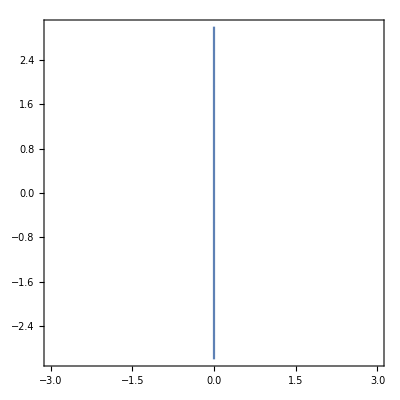

```mathematica
p1 = ContourPlot[u4 == 0 , {x,-3, 3},{y,-3,3}, Contours-> 20]
```

```mathematica
Electricfield = Grad[u4[x, y ] , {x , y}]
```

{-(-1+x)/(((-1+x)^2+y^2)^(3/2))+(1+x)/(((1+x)^2+y^2)^(3/2)),-y/(((-1+x)^2+y^2)^(3/2))+y/(((1+x)^2+y^2)^(3/2))}

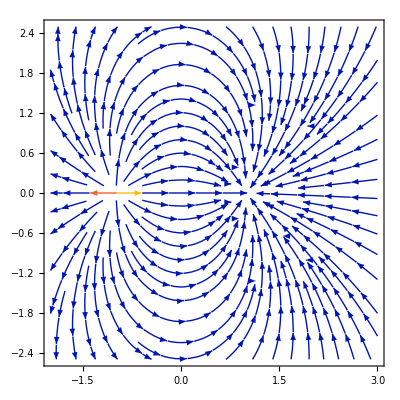

```mathematica
p2 = StreamPlot[Electricfield , {x , -2 , 3} , {y , -2.5 ,  2.5}]
```

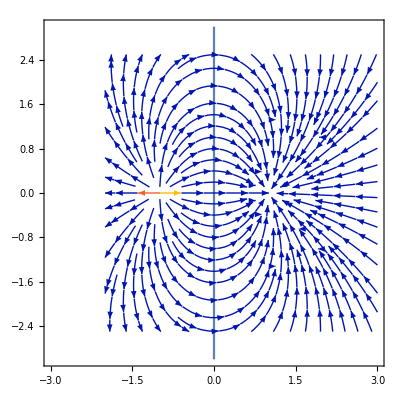

```mathematica
Show[p1 , p2]
```

# 10. Indefinite, Definite, Multiple, and Line Integrals (8)

## Indefinite Integrals

### Problem 10.1

Calculate the following indefinite integrals:

I1=∫x^a dx
I2=∫cos x dx
I3=∫(1-2x+3 x^2)/(x(1+x^2)(1+x+2 x^2))dx

#### Solution

```mathematica
Integrate[x^a,x]
```

x^(1+a)/(1+a)

```mathematica
Integrate[Cos[x],x]
```

Sin[x]

```mathematica
Integrate[(1-2x+3 x^2)/(x(1+x^2)(1+x+2 x^2)),x]
```

2 ArcTan[x]-(9 ArcTan[(1+4 x)/(√7)])/(√7)+Log[x]-1/2 Log[1+x+2 x^2]

## Definite Integrals

### Problem 10.2

Calculate (1) the exact and (2) the numerical values of the following definite integrals:

I1=∫_1^2 x^3 dx
I2=∫_1^2 cos x dx
I3=∫_1^2 (1-2x+3 x^2)/(x(1+x^2)(1+x+2 x^2))dx

#### Solution

```mathematica
Integrate[x^3 , {x , 1 , 2 }]
```

15/4

```mathematica
NIntegrate[x^3 , {x , 1 , 2 }]
```

3.75

```mathematica
Integrate[Cos[x], {x , 1 , 2 }]
```

-Sin[1]+Sin[2]

```mathematica
NIntegrate[Cos[x], {x , 1 , 2 }]
```

0.0678264

```mathematica
Integrate[(1-2x+3 x^2)/(x(1+x^2)(1+x+2 x^2)), {x , 1 , 2 }]
```

-π/2+2 ArcTan[2]+(9 ArcTan[5/(√7)])/(√7)-(9 ArcTan[9/(√7)])/(√7)+Log[4]-Log[11]/2

```mathematica
NIntegrate[(1-2x+3 x^2)/(x(1+x^2)(1+x+2 x^2)), {x , 1 , 2 }]
```

0.147868

## Multiple Integrals

### Problem 10.3

Calculate the following indefinite integral:

∫∫z(x^2+y^2) sin x cos y dx dy dz

#### Solution

```mathematica
Integrate[z(x^2+y^2) Sin [x] Cos[ y] , x,y,z]
```

1/2 z^2 (2 x Sin[x] Sin[y]-Cos[x] (2 y Cos[y]+(-4+x^2+y^2) Sin[y]))

### Problem 10.4

(1) Calculate the area of a rectangle x ∈ [-a/2,a/2] and y ∈ [-b/2,b/2] . 
(2) Show that the result is independent of the integration order.

#### Solution

```mathematica
Integrate[1 , {x , -a/2 , a/2} ,{ y , -b/2 , b/2}]
```

a b

```mathematica
Integrate[1 ,  { y , -b/2 , b/2},{x , -a/2 , a/2}]
```

a b

```mathematica
Integrate[1 , {x , -a/2 , a/2} ,{ y , -b/2 , b/2}] == Integrate[1 ,  { y , -b/2 , b/2},{x , -a/2 , a/2}]
```

True

### Problem 10.5

Caculate the area of the circle of center (0,0) and radius R 
(1) in Cartesian coordinates
(2) in polar coordinates

#### Solution

```mathematica
Evaluate[Integrate[1, {x, -R, R} , {y , -Sqrt[R ^2 - x ^ 2], Sqrt[R ^2 - x ^ 2]}]]
```

π R √(R^2)

```mathematica
Integrate[r, {r , 0 , R} , {θ , 0 , 2Pi}]
```

π R^2

### Problem 10.6

The ellipsoid is a generalization of the sphere. An ellipsoid of center (0,0,0) and semi-major axes a, b, c is defined by the following equation:

x^2/a^2+y^2/b^2+z^2/c^2=1

(1) Caculate the volume of this ellipsoid.
(2) Show that the formula gives the volume of a sphere when a=b=c. Hint: Use the replacement command “/.”.
(3) Plot the ellipsoid for a=4, b=2.5, c=1. Hint: Use the Ellipsoid command.

#### Solution

```mathematica
V=Integrate[1, {x, -a, a}, {y, -b Sqrt[1 - x^2/a^2], b Sqrt[1 - x^2/a^2]}, {z, -c Sqrt[1 - x^2/a^2 - y^2/b^2], c Sqrt[1 - x^2/a^2 - y^2/b^2]}]
```

4/3 a b c π

```mathematica
V/.{a->r,b->r,c->r}
```

(4 π r^3)/3

```mathematica
Graphics3D[Ellipsoid[{0,0,0},{4,2.5,1}],Axes->True]
```

-Graphics3D-

### Problem 10.7

Calculate the volume of the torus (see Problem 3.11) 
(1) using the Assumptions option to indicate that R>0 and r>0.  
(2) without using the Assumptions option to indicate that R>0 and r>0.
(3) In which case is the computation faster? 
Hint: (1) Cylindrical coordinates are convenient to calculate the volume of the torus, because it has rotational symmetry. (2) You can use the AbsoluteTiming command to display how much time it takes Mathematica to perform the computation

#### Solution

to avoid confusion we use ρ instead of r in cylindrical coordinates

```mathematica
Integrate[ρ,{θ,0,2Pi},{ρ,R-r,R+r},{z,-Sqrt[r^2-(ρ-R)^2],Sqrt[r^2-(ρ-R)^2]},Assumptions->{R>0,r>0}]
```

2 π^2 r^2 R

```mathematica
Integrate[ρ,{θ,0,2Pi},{ρ,R-r,R+r},{z,-Sqrt[r^2-(ρ-R)^2],Sqrt[r^2-(ρ-R)^2]}]
```

2 ⅈ π r^2 R (Log[-r]-Log[r])

```mathematica
AbsoluteTiming[%180]
```

{3.9×10^-6,2 π^2 r^2 R}

```mathematica
AbsoluteTiming[%181]
```

{4.1×10^-6,2 ⅈ π r^2 R (Log[-r]-Log[r])}

The one with assumptions is faster

## Line Integrals

### Problem 10.8

Calculate the perimenter of the ellipse defined by the following equation:

x^2/a^2+y^2/b^2=1

#### Solution

we will use arc length formula and we let 0 ≤ t ≤ 2π

```mathematica
Integrate[Sqrt[a^2 (Sin[t])^2+b^2 (Cos[t])^2],{t,0,2Pi}]
```

ConditionalExpression[2 (√(b^2) EllipticE[1-a^2/b^2]+√(a^2) EllipticE[1-b^2/a^2]), ]

# 11. Fourier Series and Transforms (3)

### Problem 11.1

Compute the 3rd order Fourier series expansion of the following functions

(1)|t| 
(2)t^2
(3)ⅇ^-t

Plot each function superimposed on its Fourier series expansion

#### Solution

```mathematica
FourierSeries[Abs[t],t,3]
```

-(2 ⅇ^(-ⅈ t))/π-(2 ⅇ^(ⅈ t))/π-(2 ⅇ^(-3 ⅈ t))/(9 π)-(2 ⅇ^(3 ⅈ t))/(9 π)+π/2

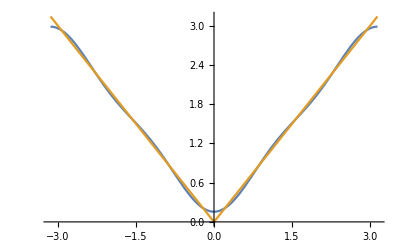

```mathematica
Plot[{Evaluate[FourierSeries[Abs[t],t,3]],Abs[t]},{t,-Pi,Pi}]
```

```mathematica
FourierSeries[t^2,t,3]
```

-2 ⅇ^(-ⅈ t)-2 ⅇ^(ⅈ t)+1/2 ⅇ^(-2 ⅈ t)+1/2 ⅇ^(2 ⅈ t)-2/9 ⅇ^(-3 ⅈ t)-2/9 ⅇ^(3 ⅈ t)+π^2/3

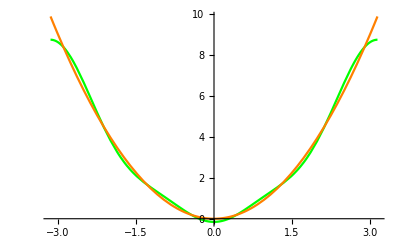

```mathematica
Plot[{Evaluate[FourierSeries[t^2,t,3]],t^2},{t,-Pi,Pi},PlotStyle->{Green,Orange}]
```

```mathematica
FourierSeries[E^-t,t,3]
```

Sinh[π]/π-((1/2+ⅈ/2) ⅇ^(-ⅈ t) Sinh[π])/π-((1/2-ⅈ/2) ⅇ^(ⅈ t) Sinh[π])/π+((1/5+(2 ⅈ)/5) ⅇ^(-2 ⅈ t) Sinh[π])/π+((1/5-(2 ⅈ)/5) ⅇ^(2 ⅈ t) Sinh[π])/π-((1/10+(3 ⅈ)/10) ⅇ^(-3 ⅈ t) Sinh[π])/π-((1/10-(3 ⅈ)/10) ⅇ^(3 ⅈ t) Sinh[π])/π

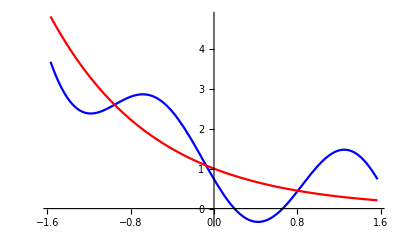

```mathematica
Plot[{Evaluate[FourierSeries[E^-t,t,3]],E^-t},{t,-Pi/2,Pi/2},PlotStyle->{Blue,Red}]
```

### Problem 11.2

Find the 3rd coefficient in the Fourier series expansions of the following functions given in Problem 11.1.

#### Solution

```mathematica
FourierCoefficient[Abs[t],t,3]
```

-2/(9 π)

```mathematica
FourierCoefficient[t^2,t,3]
```

-2/9

```mathematica
FourierCoefficient[E^-t,t,3]
```

-((1/10-(3 ⅈ)/10) Sinh[π])/π

### Problem 11.3

Compute the Fourier transforms of the following functions

(1)e^(-t^2)sin t
(2) 1/(1+t^2)
(3)1

#### Solution

```mathematica
FourierTransform[Exp[-t^2] Sin[t],t,α]
```

(ⅈ (-1+Cosh[α]+Sinh[α]) (Cosh[1/4 (1+α)^2]-Sinh[1/4 (1+α)^2]))/(2 √2)

```mathematica
FourierTransform[1/(1+t^2),t,α]
```

ⅇ^(-Abs[α]) √(π/2)

```mathematica
FourierTransform[1,t,α]
```

√(2 π) DiracDelta[α]

# 12. Analytic Functions, Contour Integrals, and Residue Theorem (5)

### Problem 12.1

Find the residues of the following functions at the specified points 
(sin π z)/(4 z^2-1) at z=1/2
1/(z^2-5z+6) at z=2
z^3/(sin (z-2)) at z=2

Note that the the ordinary Riemann definite integrals are divergent.

#### Solution

```mathematica
Residue[Sin[Pi z]/(4z^2-1),{z,1/2}]
```

1/4

```mathematica
Residue[1/(z^2-5z+6),{z,2}]
```

-1

```mathematica
Residue[z^3/(Sin[z-2]),{z,2}]
```

8

### Problem 12.2

Find the Cauchy principal values of the following integrals
∫_-1^2 1/x ⅆx
∫_1^4 1/(x-2)^5 ⅆx
∫_0^π tan xⅆx

Note that the the ordinary Riemann definite integrals are divergent.

#### Solution

```mathematica
Integrate[1/x,{x,-1,2},PrincipalValue->True]
```

Log[2]

```mathematica
Integrate[1/(x-2)^5,{x,1,4},PrincipalValue->True]
```

15/64

```mathematica
Integrate[Tan[x],{x,0,Pi},PrincipalValue->True]
```

0

### Problem 12.3

Use the commands ContourPlot and Plot3D to visualize the branch cuts of the following functions

(1) √z
(2) ln(z)

Hint:Define z=x+iy then plot the real and imaginary parts of the functions. You can set x ∈ [-10,10] and  y ∈ [-10,10]

#### Solution

```mathematica
z= x+I*y
```

x+ⅈ y

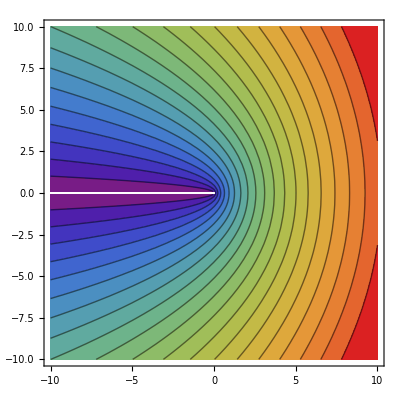

```mathematica
ContourPlot[Re[Sqrt[z]],{x,-10,10},{y,-10,10},ColorFunction->"Rainbow",Contours->20]
```

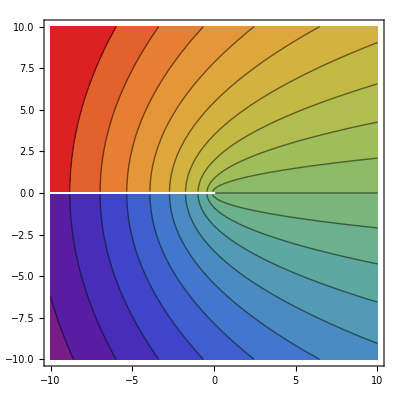

```mathematica
ContourPlot[Im[Sqrt[z]],{x,-10,10},{y,-10,10},ColorFunction->"Rainbow",Contours->20]
```

```mathematica
Plot3D[Re[Sqrt[z]],{x,-10,10},{y,-10,10},ColorFunction->Hue]
```

-Graphics3D-

```mathematica
Plot3D[Im[Sqrt[z]],{x,-10,10},{y,-10,10},ColorFunction->Hue]
```

-Graphics3D-

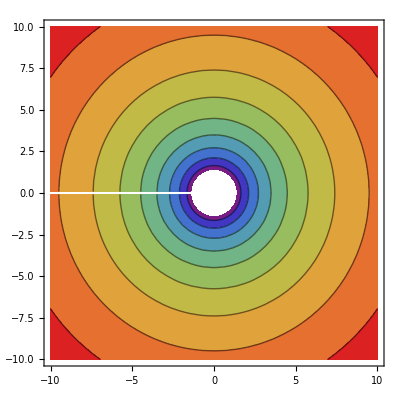

```mathematica
ContourPlot[Re[Log[z]],{x,-10,10},{y,-10,10},ColorFunction->"Rainbow"]
```

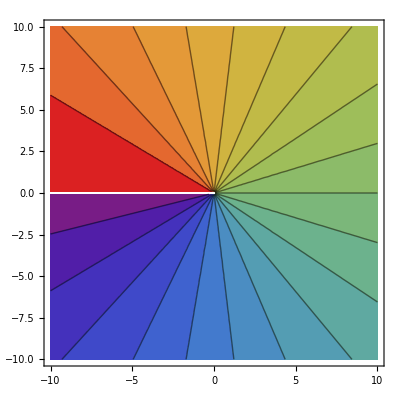

```mathematica
ContourPlot[Im[Log[z]],{x,-10,10},{y,-10,10},Contours->20,ColorFunction->"Rainbow"]
```

```mathematica
Plot3D[Re[Log[z]],{x,-10,10},{y,-10,10},ColorFunction->Hue]
```

-Graphics3D-

```mathematica
Plot3D[Im[Log[z]],{x,-10,10},{y,-10,10},ColorFunction->Hue]
```

-Graphics3D-

### Problem 12.4

Calculate the following contour integral

int1=∮_(|z|=2)  (1−e^z+z)/((z^3(z-1))^2)

(1) by using the Cauchy integral theorem
(2) by parametrizing z over the given circle

#### Solution

```mathematica
f[z_]=(1-E^z+z)/(z^3(z-1)^2)
```

(1-ⅇ^z+z)/((-1+z)^2 z^3)

we will use Residue theorem

```mathematica
int1 = 2Pi I (Residue[f[z],{z,0}]+Residue[f[z],{z,1}])
```

2 ⅈ (-11/2+2 ⅇ) π

```mathematica
Simplify[%332]
```

ⅈ (-11+4 ⅇ) π

```mathematica
f[z]/. z-> (2E^(I θ))
```

(ⅇ^(-3 ⅈ θ) (1-ⅇ^(2 ⅇ^(ⅈ θ))+2 ⅇ^(ⅈ θ)))/(8 (-1+2 ⅇ^(ⅈ θ))^2)

```mathematica
g[θ]= (ⅇ^(-3 ⅈ θ) (1-ⅇ^(2 ⅇ^(ⅈ θ))+2 ⅇ^(ⅈ θ)))/(8 (-1+2 ⅇ^(ⅈ θ))^2)
```

(ⅇ^(-3 ⅈ θ) (1-ⅇ^(2 ⅇ^(ⅈ θ))+2 ⅇ^(ⅈ θ)))/(8 (-1+2 ⅇ^(ⅈ θ))^2)

```mathematica
Integrate[g[θ]*2I E^(I θ),{θ,0,2Pi}]
```

ⅈ (-11+4 ⅇ) π

### Problem 12.5

The goal of the following problem is to reproduce Figure 10.5 of the textbook (Example 5, Section 10, Chapter 14).
The below plots show (1) equipotentials (solid lines) and (2) field lines (dashed lines) at the end of a semi-infinite capacitor.
The plates of the capacitor are at y = π and y = -π and extend over the range x ∈ (- ∞, -1].
The plots show only the y > 0 equipotentials and field lines.
Modify the given codes so that the plots show equipotentials and field lines for both y > 0 and y < 0.

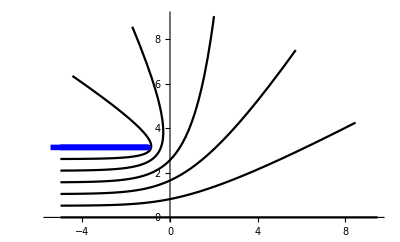

```mathematica
potplot1=ParametricPlot[{{u+Exp[u],0},{u+Exp[u]Cos[Pi/6],Pi/6+Exp[u]Sin[Pi/6]},{u+Exp[u]Cos[Pi/3],Pi/3+Exp[u]Sin[Pi/3]},{u+Exp[u]Cos[Pi/2],Pi/2+Exp[u]Sin[Pi/2]},{u+Exp[u]Cos[2Pi/3],2Pi/3+Exp[u]Sin[2Pi/3]},{u+Exp[u]Cos[5Pi/6],5Pi/6+Exp[u]Sin[5Pi/6]},{u+Exp[u]Cos[Pi],Pi+Exp[u]Sin[Pi]}},{u,-5,2.01},PlotStyle->{Black,Black,Black,Black,Black,Black,{Blue,Thickness[0.01]}}]
```

Similarly, the electric field lines

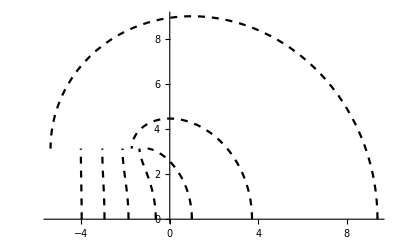

```mathematica
eplot1=ParametricPlot[{{-4+Exp[-4]Cos[v],v+Exp[-4]Sin[v]},{-3+Exp[-3]Cos[v],v+Exp[-3]Sin[v]},{-2+Exp[-2]Cos[v],v+Exp[-2]Sin[v]},{-1+Exp[-1]Cos[v],v+Exp[-1]Sin[v]},{0+Exp[0]Cos[v],v+Exp[0]Sin[v]},{1+Exp[1]Cos[v],v+Exp[1]Sin[v]},{2+Exp[2]Cos[v],v+Exp[2]Sin[v]}},{v,0,Pi},PlotStyle->{{Black,Dashed}}]
```

Equipotentials and field lines combined (showing they are always perpendicular to each other).

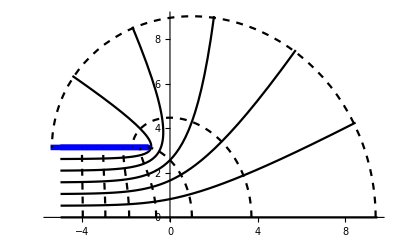

```mathematica
Show[potplot1,eplot1]
```

#### Solution

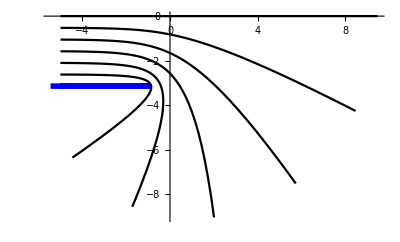

```mathematica
potplot2=ParametricPlot[{{u+Exp[u],0},{u+Exp[u]Cos[Pi/6],-Pi/6+Exp[u]Sin[-Pi/6]},{u+Exp[u]Cos[Pi/3],-Pi/3+Exp[u]Sin[-Pi/3]},{u+Exp[u]Cos[Pi/2],-Pi/2+Exp[u]Sin[-Pi/2]},{u+Exp[u]Cos[2Pi/3],-2Pi/3+Exp[u]Sin[-2Pi/3]},{u+Exp[u]Cos[5Pi/6],-5Pi/6+Exp[u]Sin[-5Pi/6]},{u+Exp[u]Cos[Pi],-Pi+Exp[u]Sin[-Pi]}},{u,-5,2.01},PlotStyle->{Black,Black,Black,Black,Black,Black,{Blue,Thickness[0.01]}}]
```

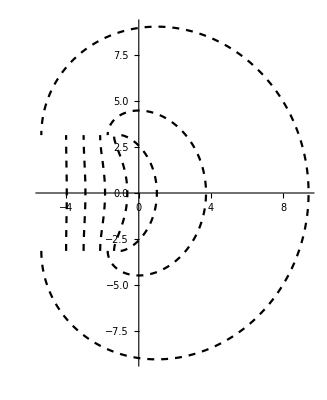

```mathematica
eplot2=ParametricPlot[{{-4+Exp[-4]Cos[v],v+Exp[-4]Sin[v]},{-3+Exp[-3]Cos[v],v+Exp[-3]Sin[v]},{-2+Exp[-2]Cos[v],v+Exp[-2]Sin[v]},{-1+Exp[-1]Cos[v],v+Exp[-1]Sin[v]},{0+Exp[0]Cos[v],v+Exp[0]Sin[v]},{1+Exp[1]Cos[v],v+Exp[1]Sin[v]},{2+Exp[2]Cos[v],v+Exp[2]Sin[v]}},{v,-Pi,Pi},PlotStyle->{{Black,Dashed}}]
```

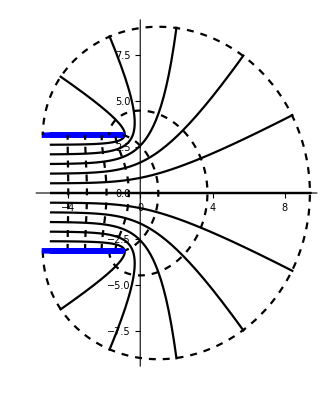

```mathematica
Show[potplot1 , eplot2 ,potplot2 ,   PlotRange-> All]
```

# 13. Legendre and Associated Legendre Polynomials (2)

### Problem 13.1

Here is Legendre’s equation

(1 - x^2) y'' - 2 x y'+ n (n + 1) y= 0

Mathematica recognizes it as being solved by Legendre polynomials (LegendreP[n,x]) and the Legendre functions of the 2nd kind (LegendreQ[n,x])

```mathematica
DSolve[(1-x^2)y''[x]-2x y'[x] + n(n+1)y[x]==0,y[x],x]
```

{{y[x]→C[1] LegendreP[n,x]+C[2] LegendreQ[n,x]}}

Calculate and plot
(1) the first 5 Legendre polynomials
(2) the first 5 Legendre functions of the 2nd kind

#### Solution

```mathematica
LegendreP[1 , x]
```

x

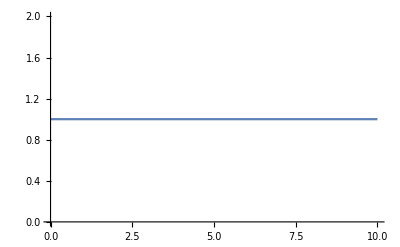

```mathematica
Plot[LegendreP[0,x],{x,0,10}]
```

```mathematica
LegendreP[2 , x]
```

1/2 (-1+3 x^2)

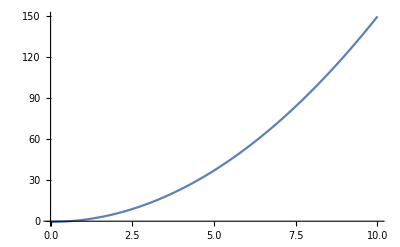

```mathematica
Plot[LegendreP[2 , x],{x,0,10}]
```

```mathematica
LegendreP[3 , x]
```

1/2 (-3 x+5 x^3)

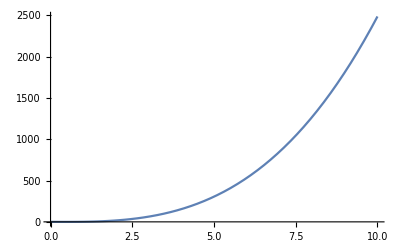

```mathematica
Plot[LegendreP[3 , x],{x,0,10}]
```

1/8 (3-30 x^2+35 x^4)

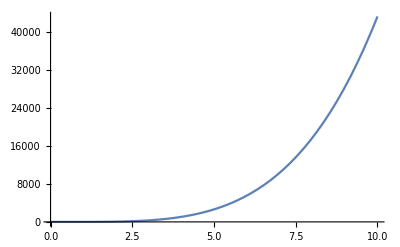

1/8 (15 x-70 x^3+63 x^5)

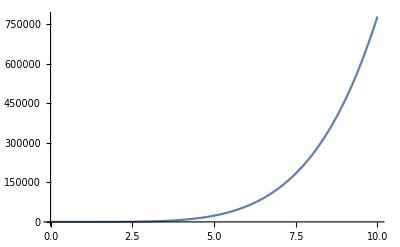

```mathematica
LegendreP[4 , x]
Plot[LegendreP[4 , x],{x,0,10}]

LegendreP[5 , x]
Plot[LegendreP[5 , x],{x,0,10}]
```

```mathematica
LegendreQ[1,x]
```

-1+x (-1/2 Log[1-x]+1/2 Log[1+x])

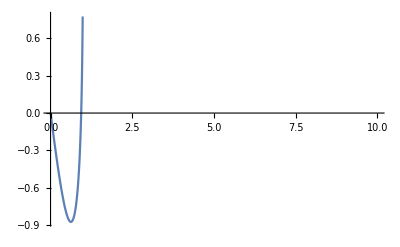

```mathematica
Plot[LegendreQ[2,x],{x,0,10}]
```

```mathematica
LegendreQ[2,x]
Plot[LegendreQ[2,x],{x,0,10}]

LegendreQ[3,x]
Plot[LegendreQ[2,x],{x,0,10}]

LegendreQ[4,x]
Plot[LegendreQ[2,x],{x,0,10}]

LegendreQ[5,x]
Plot[LegendreQ[2,x],{x,0,10}]
```

-(3 x)/2+1/2 (-1+3 x^2) (-1/2 Log[1-x]+1/2 Log[1+x])

-Graphics-

2/3-(5 x^2)/2-1/2 x (3-5 x^2) (-1/2 Log[1-x]+1/2 Log[1+x])

-Graphics-

(55 x)/24-(35 x^3)/8+1/8 (3-30 x^2+35 x^4) (-1/2 Log[1-x]+1/2 Log[1+x])

-Graphics-

-8/15+(49 x^2)/8-(63 x^4)/8+1/8 x (15-70 x^2+63 x^4) (-1/2 Log[1-x]+1/2 Log[1+x])

-Graphics-

### Problem 13.2

Here is the associated Legendre equation

(1 - x^2) y'' - 2 x y'+ (n (n + 1)- m^2/(1-x^2)) y= 0

Mathematica recognizes it as being solved by the associated Legendre polynomials (LegendreP[n,m,x]) and the Legendre functions of the 2nd kind (LegendreQ[n,m,x])

```mathematica
DSolve[(1-x^2)y''[x]-2x y'[x] + (n(n+1)-m^2/(1-x^2))y[x]==0,y[x],x]
```

{{y[x]→C[1] LegendreP[n,m,x]+C[2] LegendreQ[n,m,x]}}

Calculate and plot
(1) the associated Legendre polynomials for n=1
(2) the associated Legendre functions of the 2nd kind for n=1

#### Solution

```mathematica
LegendreP[1 , m ,   x]
```

LegendreP[1,m,x]

# 14. Bessel’s Functions (3)

### Problem 14.1

Here is Bessel’s equation

x^2 y'' +  x y'+ (x^2-p^2) y= 0

Mathematica recognizes it as being solved by Bessel’s functions of the 1st kind (BesselJ[p,x]) and Bessel’s functions of the 2nd kind (BesselY[p,x])

```mathematica
DSolve[x^2 y''[x]+x y'[x] + (x^2-p^2)y[x]==0,y[x],x]
```

{{y[x]→BesselJ[p,x] C[1]+BesselY[p,x] C[2]}}

Calculate and plot
(1) the first 4 Bessel functions of the 1st kind
(2) the first 4 Bessel functions of the 2nd kind

#### Solution

```mathematica
BesselJ[0,x]
```

BesselJ[0,x]

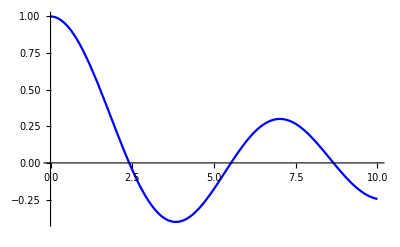

```mathematica
Plot[BesselJ[0,x],{x,0,10},PlotStyle->Blue]
```

```mathematica
BesselJ[1,x]
```

BesselJ[1,x]

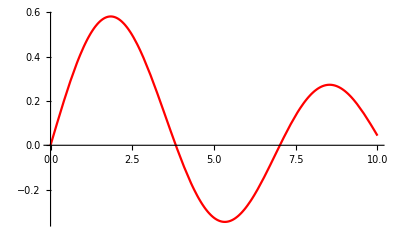

```mathematica
Plot[BesselJ[1,x],{x,0,10},PlotStyle->Red]
```

```mathematica
BesselJ[2,x]
```

BesselJ[2,x]

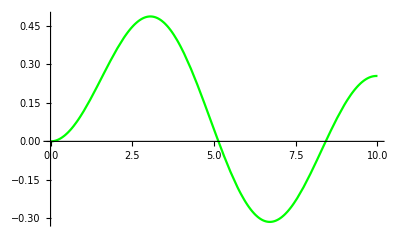

```mathematica
Plot[BesselJ[2,x],{x,0,10},PlotStyle->Green]
```

```mathematica
BesselJ[3,x]
```

BesselJ[3,x]

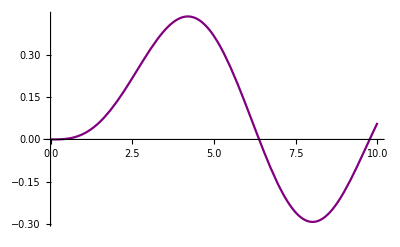

```mathematica
Plot[BesselJ[3,x],{x,0,10},PlotStyle->Purple]
```

### Problem 14.2

Find the the 2nd zero of J_0 and the 1st zero of Y_3

#### Solution

```mathematica
N[BesselJZero[0,2]]
```

5.52008

```mathematica
N[BesselYZero[3,1]]
```

4.52702

### Problem 14.3

Use Mathematica to determine the behavior of J_p(x) to zeroth order for large arguments and for small arguments. Hint: Use the Series command.

#### Solution

for large arguments

```mathematica
Series[BesselJ[p , x] , {x , Infinity ,0}]
```

Cos[-x+1/4 (1+2 p) π+O[1/x]^1] (√(2/π) √(1/x)+O[1/x]^1)

for small arguments

```mathematica
Series[BesselJ[p , x] , {x , 0 ,0}]
```

x^p (2^-p/Gamma[1+p]+O[x]^1)

# 15. The Heat Equation (1)

### Problem 15.1

(1) Use the NDSolve command to solve numerically the heat equation in 1D assuming that: 
(i) the initial state of the temperature field at t=0 is given by T(x,0)=sin((5π x)/L),  where x ∈ [0,L].
(ii) the boundary conditions are given by T(0,t)=0 and  T(L,t)=0.
(iii) the thermal diffusivity κ=0.03.
(2) Plot the solution T(x,t). 
Hint: (1) Let t ∈ [0,1] and L=1. (2) To plot the solution, use the solution as a rule and substitute it into T(x,t). Afterwards, use the Evaluate command to turn the result into a function that can plotted.

#### Solution

```mathematica
L =1 
κ=0.03
```

1

0.03

```mathematica
a = T[x, t] /. t -> 0
b =T[x, t] /. x -> 0 
c =T[x, t] /. x -> L

NDSolve[{D[T[x, t], x,x]  == 1/κ  D[T[x,t], t]   ,a == sin[(5π x)/L] , b == 0  , c == 0   },T,{x , 0 ,L} ,  {t, 0 , 1}]
```

T[x,0]

T[0,t]

T[1,t]

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve[{T^(2,0)[x,t]==33.3333 T^(0,1)[x,t],T[x,0]==sin[5 π x],T[0,t]==0,T[1,t]==0},T,{x,0,1},{t,0,1}]

```mathematica
ifun=First[T/.NDSolve[{D[T[x, t], x,x]  == 1/κ  D[T[x,t], t]   ,a == sin[(5π x)/L] , b == 0  , c == 0   },T,{x , 0 ,L} ,  {t, 0 , 1}] ]
```

```mathematica
Plot3D[ifun[x,t],{x,0,L},{t,0,1},ColorFunction->"Rainbow"]
```

-Graphics3D-

# 16. Wave Equation (1)

### Problem 16.1

Repeat Problem 15.1 for the wave equation in 1D assuming that: 
(i) the propagation velocity is 1 
(ii) the initial conditions are given by u(x,0)=Sin(x) and  (∂u(x,t))/(∂t)|_(t=0)=0.
(ii) the boundary conditions are given by u(0,t)=t sin(t) and  u(2π,t)=0.
Hint: Let t ∈ [0,10].

```mathematica
q=D[u[x,t], t]/.t->0
```

u^(0,1)[x,0]

```mathematica
NDSolve[{D[u[x,t], x,x]==D[u[x,t], t,t],u[x,0]==Sin[x],q==0, u[0,t]==t  Sin[t],u[2Pi,t]==0},u,{x,0,1},{t,0,10}]
```

{{u→InterpolatingFunction[…]}}

```mathematica
ifun=First[u/.NDSolve[{D[u[x,t], x,x]==D[u[x,t], t,t],u[x,0]==Sin[x],q==0, u[0,t]==t  Sin[t],u[2Pi,t]==0},u,{x,0,1},{t,0,10}]]
```

InterpolatingFunction[…]

```mathematica
Plot3D[ifun[x,t],{x,0,1},{t,0,10},ColorFunction->"Rainbow"]
```

-Graphics3D-

# 17. Integral Transform Solutions of PDEs (2)

### Problem 17.1

(1) Solve the following differential equation using the Laplace transform:

y''(t) + y(t) = sin(t)

(2) Compare the solution with the solution found directly using the DSolve command.

#### Solution

```mathematica
LaplaceTransform[y''[t]+y[t]==Sin[t],t,s]
```

LaplaceTransform[y[t],t,s]+s^2 LaplaceTransform[y[t],t,s]-s y[0]-y'[0]==1/(1+s^2)

```mathematica
Solve[%,LaplaceTransform[y[t],t,s]]
```

{{LaplaceTransform[y[t],t,s]→(1+s y[0]+s^3 y[0]+y'[0]+s^2 y'[0])/((1+s^2)^2)}}

```mathematica
InverseLaplaceTransform[%,s,t]
```

{{y[t]→1/2 (-t Cos[t]+Sin[t])+Cos[t] y[0]+Sin[t] y'[0]}}

```mathematica
{{y[t]->1/2 (-t Cos[t]+Sin[t])+Cos[t] y[0]+Sin[t] y'[0]}}⟦1,1,2⟧
```

```mathematica
1/2 (-t Cos[t]+Sin[t])+Cos[t] y[0]+Sin[t] y'[0]
```

1/2 (-t Cos[t]+Sin[t])+Cos[t] y[0]+Sin[t] y'[0]

```mathematica
%/.{y[0]->Subscript[c, 1],y'[0]->Subscript[c, 2]}
```

1/2 (-t Cos[t]+Sin[t])+Cos[t] c_1+Sin[t] c_2

```mathematica
DSolve[y''[t]+y[t]==Sin[t],y[t],t]
```

{{y[t]→C[1] Cos[t]+C[2] Sin[t]+1/4 (-2 t Cos[t]-2 Cos[t]^2 Sin[t]+Cos[t] Sin[2 t])}}

```mathematica
{{y[t]->C[1] Cos[t]+C[2] Sin[t]+1/4 (-2 t Cos[t]-2 Cos[t]^2 Sin[t]+Cos[t] Sin[2 t])}}⟦1,1,2⟧
```

C[1] Cos[t]+C[2] Sin[t]+1/4 (-2 t Cos[t]-2 Cos[t]^2 Sin[t]+Cos[t] Sin[2 t])

```mathematica
Simplify[C[1] Cos[t]+C[2] Sin[t]+1/4 (-2 t Cos[t]-2 Cos[t]^2 Sin[t]+Cos[t] Sin[2 t])]
```

(-t/2+C[1]) Cos[t]+C[2] Sin[t]

they are the same but of different form

### Problem 17.2

(1) Solve the following differential equation using the Fourier transform:

y''(t) + y(t) = sin(t)

(2) Compare the solution with the solutions found directly using the DSolve command and the solution found using the Laplace transform in Problem 17.1 .

#### Solution

```mathematica
Clear[u]
```

```mathematica
Solve[u - E^(u) == -1 , u]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{u→0}}